```mathematica
α = 0.0072973525693;
Subscript[m, e]=510998.95;(*eV*)
Subscript[m, p] = 938.27208816×10^6;(*eV*)
Subscript[ϵ, 0]=13.6;(*eV*)
Subscript[T, 0]=2.34865477×10^-4;(*eV*)
Subscript[m, pl]=1.2211×10^28;(*eV*)
Subscript[Ω, m]=0.315;
Subscript[Ω, b]=0.04924319136;
Subscript[ρ, c] = 3.679272179×10^-11;(*eV^4*)
μ = 1217285022;(*eV*)
effdof = 2+6×7/8×(4/11)^(4/3); (*effective degrees of freedom, only including photons and neutrinos*)
Subscript[σ, T] = (8×Pi×α^2)/(3×Subscript[m, e]^2) ;(*eV^-2*)
Subscript[ρ, b0] = Subscript[Ω, b]×Subscript[ρ, c];
Subscript[k, B] = 8.617333262145×10^-5(*eV K^-1*)
```

```mathematica
(*baryon number density*)
nb[z_] := Subscript[Ω, b]×Subscript[ρ, c]/Subscript[m, p]×(1+z)^3
(* photon energy density*)
rhog[z_] := (2×Pi^2)/30×(Subscript[T, 0]×(1+z))^4
(*baryon energy density*)
rhob[z_] := Subscript[ρ, b0]×(1+z)^3
(*recombination rate*)
recrate[z_] := 9.78×(α^2/Subscript[m, e]^2)×Sqrt[Subscript[ϵ, 0]/Tb[z]]×Log[Subscript[ϵ, 0]/Tb[z]]
(*ionisation rate*)
ionrate[z_] := 9.78×(α^2/Subscript[m, e]^2)×Sqrt[Subscript[ϵ, 0]/Tb[z]]×Log[Subscript[ϵ, 0]/Tb[z]]×((Subscript[m, e]×Tb[z])/(2×Pi))^(3/2)×Exp[-Subscript[ϵ, 0]/Tb[z]]
(*hubble rate*)
hubble[z_] := Sqrt[(8×Pi)/(3×Subscript[m, pl]^2)×(Subscript[Ω, m] ×Subscript[ρ, c] ×(1+z)^3+(effdof×Pi^2)/30×(Subscript[T, 0]×(1+z))^4)]
```

```mathematica
(*Exact solution*)
```

```mathematica
Xdiff[z_] := -((1-xe[z])×ionrate[z] - (xe[z])^2×nb[z]×recrate[z])/((1+z)×hubble[z])
Tbdiff[z_] :=  2×Tb[z]/(1+z)-((8/3×μ/Subscript[m, e]×(2×Pi^2)/(30×Subscript[m, p])×(Subscript[T, 0]×(1+z))^4×xe[z]/(1+z))×Subscript[σ, T]×(Subscript[T, 0]×(1+z)-Tb[z]))/hubble[z]
```

```mathematica
Subscript[z, i] = 0;
Subscript[z, f] = 1900;
sol = NDSolve[{xe'[z]==Xdiff[z],Tb'[z]==Tbdiff[z], xe[Subscript[z, f]]==1, Tb[Subscript[z, f]]==Subscript[T, 0]×(1+Subscript[z, f])}, {xe[z],Tb[z]}, {z,Subscript[z, i],Subscript[z, f]}]
```

{{xe[z]→InterpolatingFunction[…][z],Tb[z]→InterpolatingFunction[…][z]}}

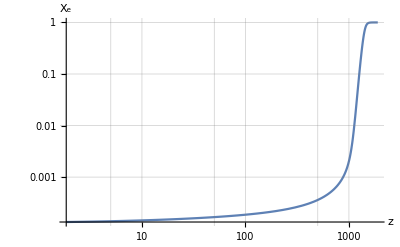

```mathematica
LogLogPlot[Evaluate[xe[z]/.sol[[1]]], {z,Subscript[z, i],Subscript[z, f]},AxesLabel->{"z","X_e"},GridLines->Automatic,PlotRange->All]
```

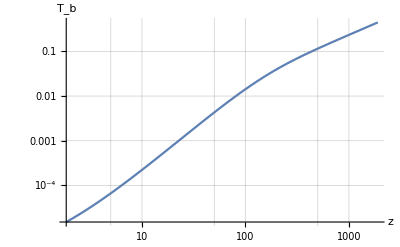

```mathematica
LogLogPlot[Evaluate[Tb[z]/.sol[[1]]],{z,Subscript[z, i],Subscript[z, f]},AxesLabel->{"z","T_b"},GridLines->Automatic,PlotRange->All]
```

```mathematica
Subscript[X, e][z_] := xe[z]/.sol[[1]]
```

```mathematica
Subscript[X, e][z]/.{z->Subscript[z, i]}
```

0.000129956